# Genetic programming

## Expression representation

```mathematica
GetLabelName[label_]:=Replace[label,Framed[Style[labelName_,___],___]:>labelName];

FunctionToGraph[expr_]:=Block[{tree,labels,functionNames,terminalNames,vertexLabels,order,pos},
tree = ToExpression@ToBoxes@TreeForm[expr];
labels=Cases[tree,Inset[name_,n_]:>Rule[n,GetLabelName[name]],Infinity] /.HoldForm[f_]:>f;
functionNames = DeleteDuplicates@Cases[expr,f_[_,_]:>f,All];
terminalNames = Complement[DeleteDuplicates[labels[[All,2]]],functionNames];
vertexLabels = labels /.Join[Thread[functionNames->Map[Func,functionNames]], Thread[terminalNames->Map[Term,terminalNames]]];

{order,pos}=Catenate/@Cases[tree,Line[order_]|GraphicsComplex[pos_,___]:>{order,pos},Infinity];
{Graph[DirectedEdge@@@order,VertexLabels->labels],vertexLabels}
];
GraphToFunction[edgeList_,vertexLabels_]:=Block[{depthFirstScan},
depthFirstScan = Reverse@First@Last@Reap@DepthFirstScan[edgeList,1,{"PostvisitVertex"->(Sow[#]&)}] /. vertexLabels;

First@FixedPoint[SequenceReplace[#,{Func[f_],Term[y_],Term[x_]}:>Term[f[x,y]]]&,depthFirstScan]/.Term[x_]:>x
];
```

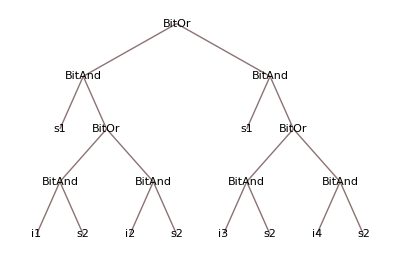

```mathematica
TreeForm[BitOr[BitAnd[s1,BitOr[BitAnd[i3,s2],BitAnd[i4,s2]]],BitAnd[s1,BitOr[BitAnd[i1,s2],BitAnd[i2,s2]]]]]
```

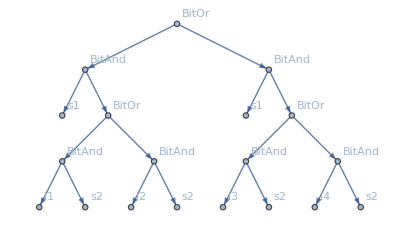
{-Graphics-,{1→Func[BitOr],2→Func[BitAnd],3→Term[s1],4→Func[BitOr],5→Func[BitAnd],6→Term[i1],7→Term[s2],8→Func[BitAnd],9→Term[i2],10→Term[s2],11→Func[BitAnd],12→Term[s1],13→Func[BitOr],14→Func[BitAnd],15→Term[i3],16→Term[s2],17→Func[BitAnd],18→Term[i4],19→Term[s2]}}

```mathematica
FunctionToGraph[BitOr[BitAnd[s1,BitOr[BitAnd[i1,s2],BitAnd[i2,s2]]],BitAnd[s1,BitOr[BitAnd[i3,s2],BitAnd[i4,s2]]]]]
```

```mathematica
GraphToFunction[
-Graphics-,
{1->Func[BitOr],2->Func[BitAnd],3->Term[s1],4->Func[BitOr],5->Func[BitAnd],6->Term[i1],7->Term[s2],8->Func[BitAnd],9->Term[i2],10->Term[s2],11->Func[BitAnd],12->Term[s1],13->Func[BitOr],14->Func[BitAnd],15->Term[i3],16->Term[s2],17->Func[BitAnd],18->Term[i4],19->Term[s2]}
]
```

BitOr[BitAnd[s1,BitOr[BitAnd[i1,s2],BitAnd[i2,s2]]],BitAnd[s1,BitOr[BitAnd[i3,s2],BitAnd[i4,s2]]]]

## Operations on trees

```mathematica
Subtree[graph_,labels_,vertex_]:=Block[{children,toDelete,subtree,sublabels},
children = First@Last@Reap@DepthFirstScan[graph,vertex,{"PrevisitVertex"->(Sow[#]&)}];
toDelete = Complement[VertexList[graph],children];
subtree = VertexDelete[graph,Complement[VertexList[graph],children]];
sublabels = Cases[labels,x_/;MemberQ[children,First[x]]];

{subtree,sublabels}
];
FormatLabels[labels_]:=ReplaceAll[labels,{Term[x_]:>x,Func[x_]:>x}];
DeleteSubtree[graph_,labels_,vertex_]:=Block[{subtree,sublabels,subVertexes,conectionRemoved,withoutSubtree,newLabels},
{subtree,sublabels} = Subtree[graph, labels, vertex];
subVertexes = VertexList[subtree];
conectionRemoved = ReplaceAll[EdgeList[graph],((x_/;!MemberQ[subVertexes,x])->(y_/;MemberQ[subVertexes,y])):>x->Empty];
withoutSubtree = If[Length[Intersection[VertexList[conectionRemoved],subVertexes]]≠ 0,
VertexDelete[conectionRemoved,subVertexes],
conectionRemoved
];
newLabels = Complement[labels,sublabels];

{Graph[withoutSubtree,VertexLabels->FormatLabels[newLabels]],newLabels}
];
InsertSubtree[graph_,labels_,subtree_,sublabels_,subtreeRoot_]:=Block[{edges,missing,missingRules,newRules,insertionRules,formattedSubtree,formattedSublabels,formattedSubtreeRoot,newTree,newLabels},
If[!MemberQ[VertexList[graph],Empty],Return[$Failed]];

edges = DeleteCases[VertexList[graph],Empty];
missing = Complement[Range[Max[edges]],edges];
missingRules = Thread[Take[VertexList[subtree],UpTo[Length[missing]]]->Take[missing,UpTo[Length[VertexList[subtree]]]]];
If[Length[VertexList[subtree]]-Length[missing]>0,
newRules = Thread[Drop[VertexList[subtree],Length[missing]]-> Range[Max[edges]+1,Max[edges]+Length[VertexList[subtree]]-Length[missing]]];
insertionRules = Join[missingRules,newRules];
,
insertionRules = missingRules;
];

formattedSubtree = EdgeList[subtree]/.insertionRules;
formattedSublabels = sublabels/.insertionRules;
formattedSubtreeRoot = subtreeRoot /.insertionRules;
newTree = ReplaceAll[Join[EdgeList[graph],formattedSubtree],Empty->formattedSubtreeRoot];
newLabels = SortBy[Join[labels,formattedSublabels],First];

{Graph[newTree,VertexLabels->FormatLabels[newLabels]],newLabels}
];
```

```mathematica
f1 = LogicOr[LogicAnd[s1,LogicOr[LogicAnd[i3,s2],LogicAnd[i4,s2]]],LogicAnd[s1,LogicOr[LogicAnd[i1,s2],LogicAnd[i2,s2]]]];
f2 = LogicOr[LogicAnd[s1,LogicOr[LogicOr[i3,s2],LogicAnd[i4,s2]]],LogicXor[s1,s2]];
```

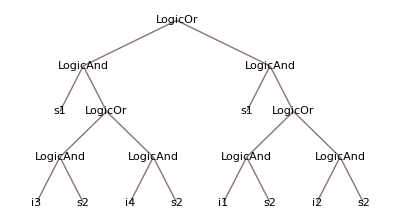
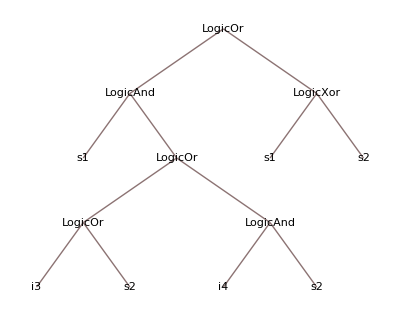

```mathematica
Map[TreeForm,{f1,f2}]
```

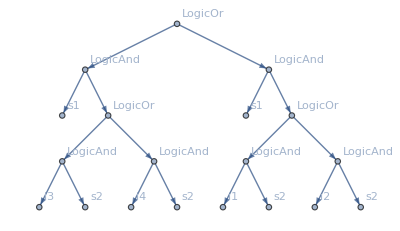
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
{g1,l1} = FunctionToGraph[f1]
```

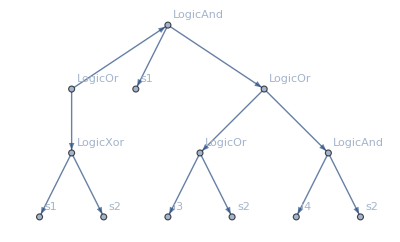
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicOr],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicXor],12→Term[s1],13→Term[s2]}}

```mathematica
{g2,l2} = FunctionToGraph[f2]
```

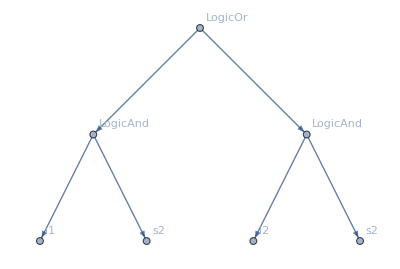
{-Graphics-,{13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
{sg1,sl1} = Subtree[g1,l1,13]
```

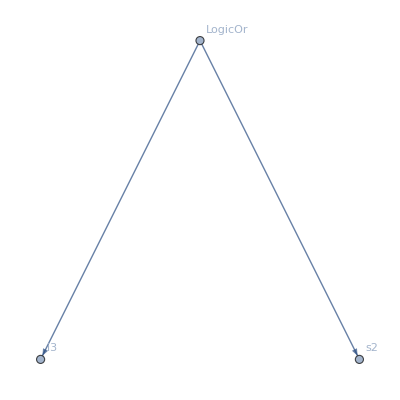
{-Graphics-,{5→Func[LogicOr],6→Term[i3],7→Term[s2]}}

```mathematica
{sg2,sl2} = Subtree[g2,l2,5]
```

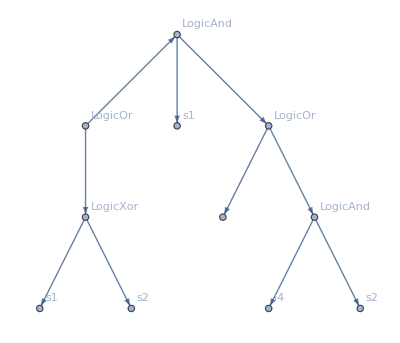
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicXor],12→Term[s1],13→Term[s2]}}

```mathematica
{dst,dl} = DeleteSubtree[g2,l2,5]
```

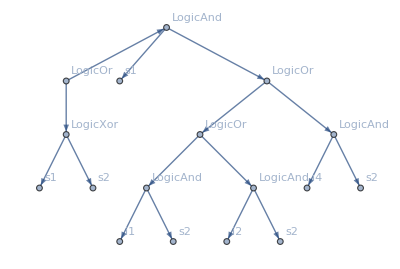
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicOr],6→Func[LogicAnd],7→Func[LogicAnd],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicXor],12→Term[s1],13→Term[s2],14→Term[i1],15→Term[s2],16→Term[i2],17→Term[s2]}}

```mathematica
InsertSubtree[dst,dl,sg1,sl1,13]
```

```mathematica
Apply[GraphToFunction,InsertSubtree[dst,dl,sg1,sl1,13]]
```

LogicOr[LogicAnd[s1,LogicOr[LogicOr[LogicAnd[i1,s2],LogicAnd[i2,s2]],LogicAnd[i4,s2]]],LogicXor[s1,s2]]

## Crossover

```mathematica
Crossover[graph1_,labels1_,graph2_,labels2_]:=Block[{vertex1,vertex2,cropped,sub},
vertex1 = RandomChoice[Drop[VertexList[graph1],1]];
vertex2 = RandomChoice[VertexList[graph2]];
cropped = DeleteSubtree[graph1,labels1,vertex1];
sub = Subtree[graph2,labels2,vertex2];

InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub],vertex2]
];
PopulationCrossover[population_,childrenPerCouple_]:=Block[{parts},
parts = Partition[RandomSample[population],2];
Apply[Join,Table[Map[Apply[Crossover,Flatten[#,1]]&,parts],childrenPerCouple]]
];
```

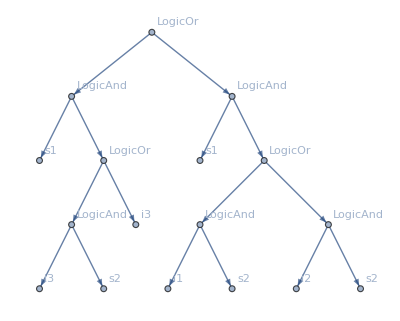
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Term[i3],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
Crossover[g1,l1,g2,l2]
```

## Mutation

```mathematica
TreeMutation[graph_,labels_]:=Block[{vertex1,vertex2,cropped,sub},
{vertex1,vertex2} = RandomSample[Drop[VertexList[graph],1],2];
cropped = DeleteSubtree[graph,labels,vertex1];
sub = Subtree[graph,labels,vertex2];

InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub],vertex2]
];
TerminalMutation[labels_,terminalSet_]:=Block[{replacePos,availableTerminals},
replacePos = RandomChoice[Cases[labels,(x_->_Term):>x]];
availableTerminals = Complement[terminalSet,Cases[labels,(replacePos->t_):>t]];

ReplaceAll[labels, (replacePos->_)->(replacePos->RandomChoice[availableTerminals])]
];
FunctionMutation[labels_,functionSet_]:=Block[{replacePos,availableFunctions},
replacePos = RandomChoice[Cases[labels,(x_->_Func):>x]];
availableFunctions = Complement[functionSet,Cases[labels,(replacePos->t_):>t]];

ReplaceAll[labels, (replacePos->_)->(replacePos->RandomChoice[availableFunctions])]
];
SymbolMutation[labels_,terminalSet_,functionSet_]:=FunctionMutation[TerminalMutation[labels,terminalSet],functionSet];
Mutation[graph_,labels_,terminalSet_,functionSet_]:=If[RandomReal[]≥0.5,TreeMutation[graph,labels],{graph,SymbolMutation[labels,terminalSet,functionSet]}];
PopulationMutate[population_,probability_,terminalSet_,functionSet_]:=Map[If[RandomReal[]<probability,Mutation[First[#],Last[#],terminalSet,functionSet],#]&,population];
```

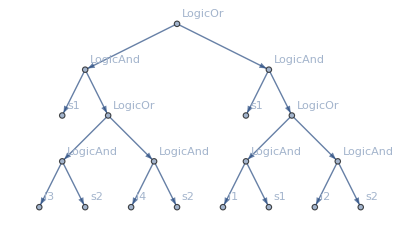
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s1],17→Func[LogicAnd],18→Term[i2],19→Term[s2]}}

```mathematica
TreeMutation[g1,l1]
```

```mathematica
SymbolMutation[l1, {Term[s1],Term[s2],Term[i1],Term[i2],Term[i3],Term[i4]},{Func[LogicOr],Func[LogicAnd],Func[LogicXor]}]
```

{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Term[i4],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicXor],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[i3]}

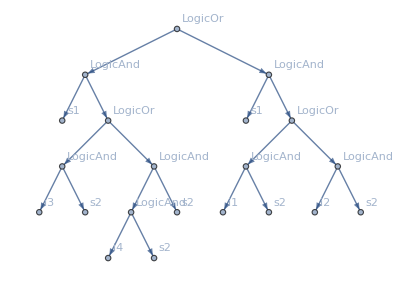
{-Graphics-,{1→Func[LogicOr],2→Func[LogicAnd],3→Term[s1],4→Func[LogicOr],5→Func[LogicAnd],6→Term[i3],7→Term[s2],8→Func[LogicAnd],9→Func[LogicAnd],10→Term[s2],11→Func[LogicAnd],12→Term[s1],13→Func[LogicOr],14→Func[LogicAnd],15→Term[i1],16→Term[s2],17→Func[LogicAnd],18→Term[i2],19→Term[s2],20→Term[i4],21→Term[s2]}}

```mathematica
Mutation[g1,l1, {Term[s1],Term[s2],Term[i1],Term[i2],Term[i3],Term[i4]},{Func[LogicOr],Func[LogicAnd],Func[LogicXor]}]
```

## Fitness function

```mathematica
EvaluateFunction[expr_,expectedOutput_]:=Block[{inputs,testInput,testFunctions,testResults,matchs,i1,i2,i3,i4,s1,s2},
inputs = Thread[{i1,i2,i3,i4}->expectedOutput];
testInput = Map[Join[inputs,#]&,Map[Thread[{s1,s2}->#]&,Tuples[{0,1},2]]];
testFunctions = Map[expr/.#&,testInput];
testResults = testFunctions/.{LogicOr->BitOr,LogicAnd->BitAnd,LogicXor->BitXor};
matchs = Map[Apply[Equal,#]&,Transpose[{expectedOutput ,testResults}]];

Count[matchs,True]/Length[matchs]
];
EvaluatePopulation[population_,expectedOutput_]:=Block[{populationAsFunctions,scores},
populationAsFunctions = Map[Apply[GraphToFunction,#]&,population];
scores = Map[EvaluateFunction[#,expectedOutput]&,populationAsFunctions];

MapThread[<|"Genome"->#1,"Score"->#2|>&,{population,scores}]
];
```

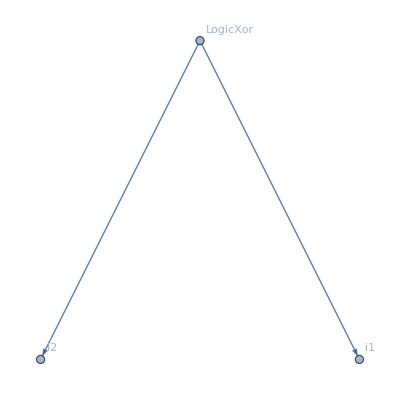
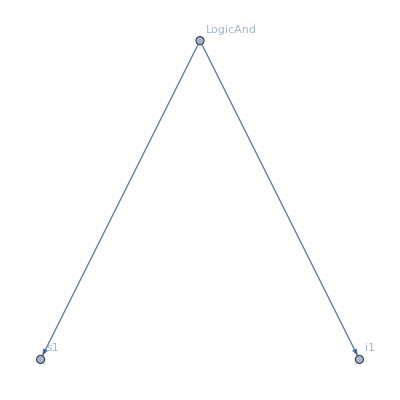
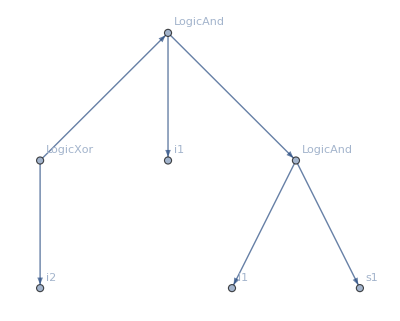
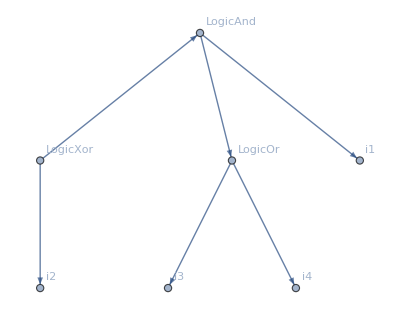
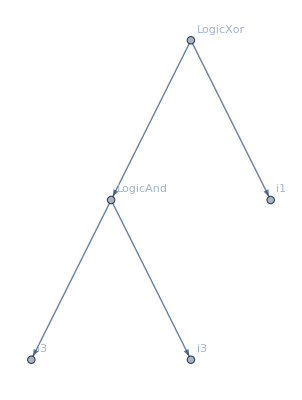
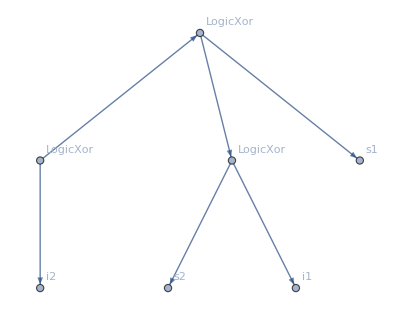
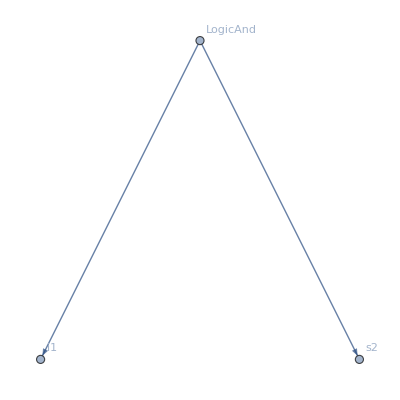
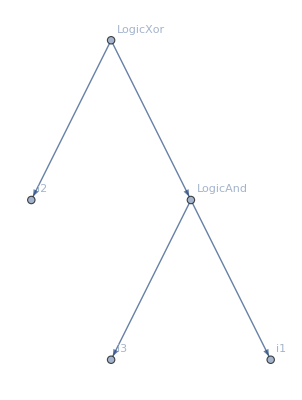
{<|Genome→{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Term[i1]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicAnd],2→Term[s1],3→Term[i1]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Func[LogicAnd],4→Term[i1],5→Func[LogicAnd],6→Term[i1],7→Term[s1]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Func[LogicAnd],4→Func[LogicOr],5→Term[i1],6→Term[i3],7→Term[i4]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicAnd],3→Term[i1],4→Term[i3],5→Term[i3]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Func[LogicXor],4→Func[LogicXor],5→Term[s1],6→Term[s2],7→Term[i1]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicAnd],2→Term[i1],3→Term[s2]}},Score→0|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Func[LogicAnd],4→Term[i1],5→Func[LogicAnd],6→Term[i1],7→Term[s1]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Func[LogicAnd],4→Term[i3],5→Term[i1]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Term[s1],3→Term[i3]}},Score→1/2|>}

```mathematica
evaluated = EvaluatePopulation[population,{1,0,1,0}]
```

## Population initialization

```mathematica
GenerateSeed[terminalSet_,functionSet_]:=Block[{head,args,labels,graph},
head = RandomChoice[functionSet];
args = RandomSample[terminalSet,2];
labels = Thread[Range[3]->Join[{head},args]];
graph = Graph[{1->2,1->3},VertexLabels->FormatLabels[Thread[Range[3]->Join[{head},args]]]];

{graph,labels}
];
GenerateInitialPopulation[size_,terminalSet_,functionSet_,recombinations_,expectedOutput_]:=Block[{seeds,population},
seeds = Table[GenerateSeed[terminalSet,functionSet],size];
population = Nest[PopulationCrossover[#,2]&,seeds,recombinations];

EvaluatePopulation[population,expectedOutput]
];
```

```mathematica
terminalSet = {Term[s1],Term[s2],Term[i1],Term[i2],Term[i3],Term[i4]};
functionSet = {Func[LogicOr],Func[LogicAnd],Func[LogicXor]};
```

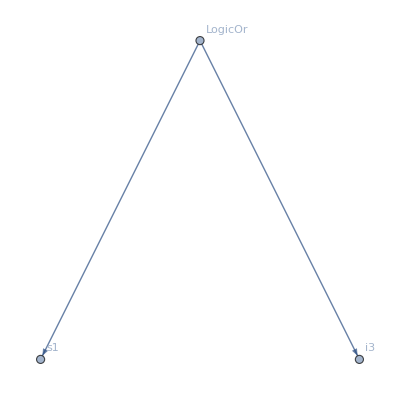
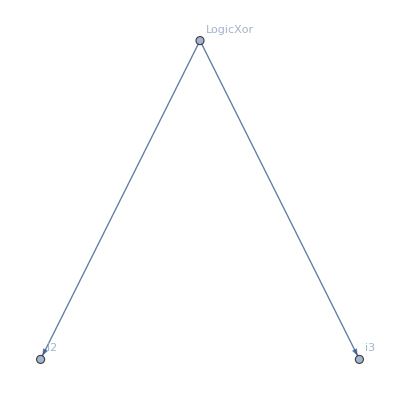
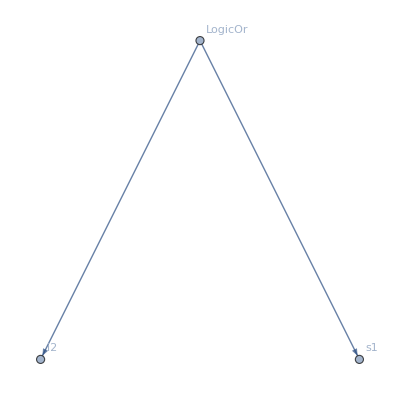
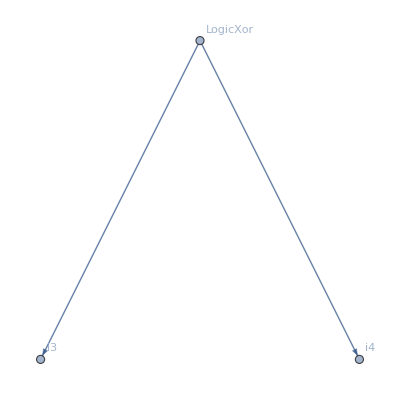
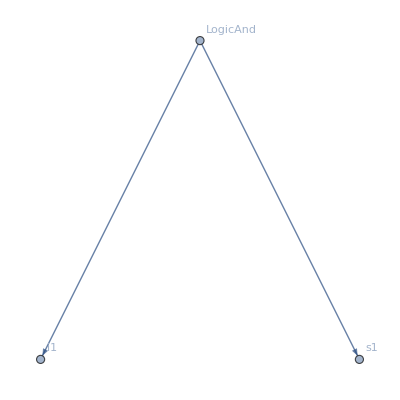
{<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[s1],3→Term[i3]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Term[i3]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i2],3→Term[s1]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Term[i3],3→Term[i4]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicAnd],2→Term[i1],3→Term[s1]}},Score→1/2|>}

```mathematica
population = GenerateInitialPopulation[5,terminalSet,functionSet,0,{0,1,0,1}]
```

## Selection

```mathematica
ProportionateSelectionIndexes[population_,n_]:=RandomSample[Reverse[Range[population]]->Range[population],n];

ProportionateRankedSelection[evaluatedGenome_,n_]:= Part[Reverse@SortBy[evaluatedGenome,Key["Score"]],ProportionateSelectionIndexes[Length[evaluatedGenome],n]]
```

```mathematica
ProportionateRankedSelection[evaluated,3]
```

{<|Genome→{-Graphics-,{1→Func[LogicAnd],2→Term[s1],3→Term[i1]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Term[s1],3→Term[i3]}},Score→1/2|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Term[i2],3→Func[LogicAnd],4→Term[i3],5→Term[i1]}},Score→1/2|>}

## Main algorithm

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]]
```

```mathematica
Generation[population_,terminalSet_,functionSet_,survivors_,mutationProb_,expectedOutput_]:=Block[{evaluated,fittest,newGeneration,mutated,childrenPerCouple},
fittest = ProportionateRankedSelection[population,survivors];
childrenPerCouple = (2 Length[population])/survivors;
newGeneration = PopulationCrossover[fittest[[All,"Genome"]],childrenPerCouple];
mutated = PopulationMutate[newGeneration,mutationProb,terminalSet,functionSet];

EvaluatePopulation[mutated,expectedOutput]
];
GeneticOptimize[population_,terminalSet_,functionSet_,survivors_,mutationProb_,expectedOutput_,generations_]:=
ProgressNestList[
Generation[#,terminalSet,functionSet,survivors,mutationProb,expectedOutput]&,
population,generations,
"Label"->"Generation"
];
```

```mathematica
terminalSet = {Term[s1],Term[s2],Term[i1],Term[i2],Term[i3],Term[i4]};
```

```mathematica
functionSet = {Func[LogicOr],Func[LogicAnd],Func[LogicXor]};
```

```mathematica
output = {1,1,0,1};
```

```mathematica
population = GenerateInitialPopulation[30,terminalSet,functionSet,0,output];
```

```mathematica
optimization = GeneticOptimize[population,terminalSet, functionSet, 10,0.3,output,10] ;
```

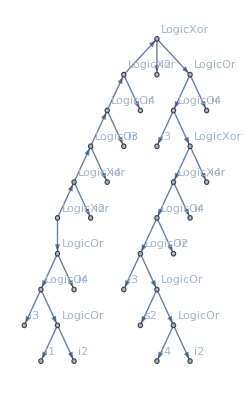
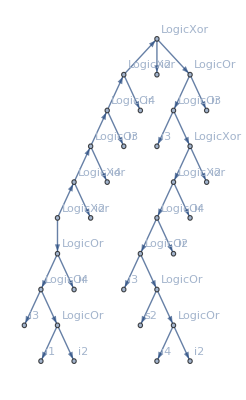
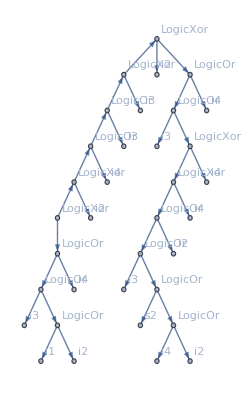
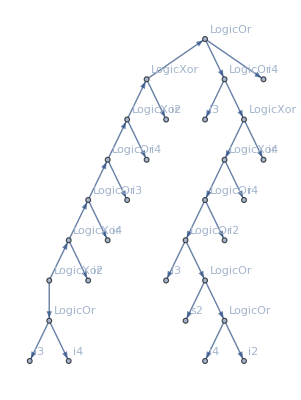
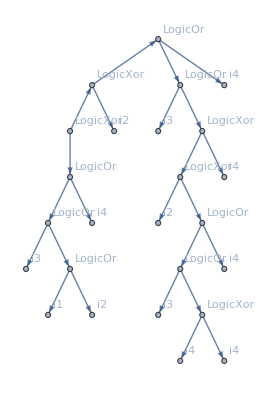
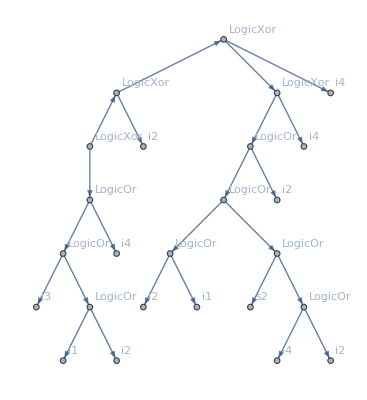
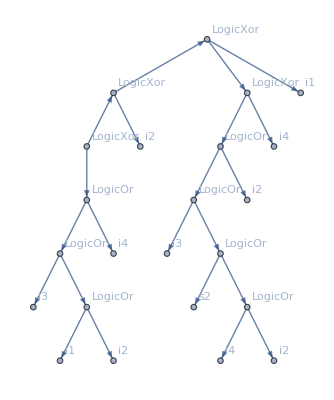
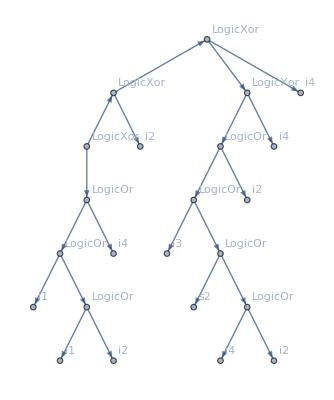
{<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Func[LogicOr],7→Term[i4],8→Func[LogicOr],9→Term[i4],10→Term[i3],11→Func[LogicXor],12→Func[LogicXor],13→Term[i4],14→Term[i3],15→Func[LogicOr],16→Term[i1],17→Term[i2],18→Term[i2],19→Func[LogicOr],20→Func[LogicOr],21→Term[i4],22→Term[i3],23→Func[LogicXor],24→Func[LogicXor],25→Term[i4],26→Func[LogicOr],27→Term[i4],28→Func[LogicOr],29→Term[i2],30→Term[i3],31→Func[LogicOr],32→Term[s2],33→Func[LogicOr],34→Term[i4],35→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Func[LogicOr],7→Term[i4],8→Func[LogicOr],9→Term[i4],10→Term[i3],11→Func[LogicXor],12→Func[LogicXor],13→Term[i4],14→Term[i3],15→Func[LogicOr],16→Term[i1],17→Term[i2],18→Term[i2],19→Func[LogicOr],20→Func[LogicOr],21→Term[i3],22→Term[i3],23→Func[LogicXor],24→Func[LogicXor],25→Term[i2],26→Func[LogicOr],27→Term[i4],28→Func[LogicOr],29→Term[i2],30→Term[i3],31→Func[LogicOr],32→Term[s2],33→Func[LogicOr],34→Term[i4],35→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Func[LogicOr],7→Term[i4],8→Func[LogicOr],9→Term[i4],10→Term[i3],11→Func[LogicXor],12→Func[LogicXor],13→Term[i3],14→Term[i3],15→Func[LogicOr],16→Term[i1],17→Term[i2],18→Term[i2],19→Func[LogicOr],20→Func[LogicOr],21→Term[i4],22→Term[i3],23→Func[LogicXor],24→Func[LogicXor],25→Term[i4],26→Func[LogicOr],27→Term[i4],28→Func[LogicOr],29→Term[i2],30→Term[i3],31→Func[LogicOr],32→Term[s2],33→Func[LogicOr],34→Term[i4],35→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Term[i3],7→Term[i4],8→Func[LogicOr],9→Term[i4],10→Term[i3],11→Func[LogicXor],12→Func[LogicXor],13→Term[i4],18→Term[i2],19→Func[LogicOr],20→Func[LogicOr],21→Term[i4],22→Term[i3],23→Func[LogicXor],24→Func[LogicXor],25→Term[i4],26→Func[LogicOr],27→Term[i4],28→Func[LogicOr],29→Term[i2],30→Term[i3],31→Func[LogicOr],32→Term[s2],33→Func[LogicOr],34→Term[i4],35→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Func[LogicOr],7→Term[i4],8→Func[LogicOr],9→Term[i4],10→Term[i3],11→Func[LogicXor],12→Func[LogicXor],13→Term[i4],14→Term[i3],15→Func[LogicOr],16→Term[i1],17→Term[i2],18→Term[i2],19→Func[LogicOr],20→Func[LogicOr],21→Term[i4],22→Term[i3],23→Func[LogicXor],24→Term[i4],25→Term[i4]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicXor],6→Func[LogicOr],7→Term[i4],8→Func[LogicXor],9→Term[i4],10→Func[LogicOr],11→Term[i4],12→Func[LogicOr],13→Term[i2],14→Term[i3],15→Func[LogicOr],16→Term[i1],17→Term[i2],18→Func[LogicOr],19→Func[LogicOr],20→Term[s2],21→Func[LogicOr],22→Term[i4],23→Term[i2],24→Term[i2],25→Term[i1]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicXor],6→Func[LogicOr],7→Term[i4],8→Func[LogicXor],9→Term[i1],10→Func[LogicOr],11→Term[i4],12→Func[LogicOr],13→Term[i2],14→Term[i3],15→Func[LogicOr],16→Term[i1],17→Term[i2],18→Term[i3],19→Func[LogicOr],20→Term[s2],21→Func[LogicOr],22→Term[i4],23→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicXor],6→Func[LogicOr],7→Term[i4],8→Func[LogicXor],9→Term[i4],10→Func[LogicOr],11→Term[i4],12→Func[LogicOr],13→Term[i2],14→Term[i1],15→Func[LogicOr],16→Term[i1],17→Term[i2],18→Term[i3],19→Func[LogicOr],20→Term[s2],21→Func[LogicOr],22→Term[i4],23→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Func[LogicXor],7→Func[LogicXor],8→Term[i3],9→Func[LogicOr],10→Term[i2],11→Func[LogicOr],12→Term[s2],13→Func[LogicOr],14→Term[i2],15→Term[i2],16→Term[i3],17→Func[LogicOr],18→Term[i2],19→Func[LogicOr],20→Term[s2],21→Func[LogicOr],22→Term[i2],23→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Func[LogicOr],5→Func[LogicOr],6→Term[i3],7→Func[LogicOr],8→Term[i2],9→Term[i2],10→Term[i3],11→Func[LogicOr],12→Term[i2],13→Func[LogicXor],14→Term[i3],15→Func[LogicOr],16→Term[i3],17→Func[LogicOr],18→Func[LogicOr],19→Func[LogicOr],20→Term[i2],21→Term[i2],22→Term[i2],23→Term[i1]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Func[LogicOr],5→Func[LogicOr],6→Func[LogicOr],7→Func[LogicOr],8→Term[i2],9→Term[i2],10→Term[i3],11→Func[LogicOr],12→Term[i2],13→Func[LogicXor],14→Term[i3],15→Func[LogicOr],16→Term[i3],17→Func[LogicOr],18→Term[i3],19→Func[LogicOr],20→Term[i2],21→Term[i2],22→Term[i2],23→Term[i1]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Func[LogicOr],7→Term[i4],8→Func[LogicOr],9→Term[i4],10→Term[i3],11→Func[LogicOr],12→Term[i4],13→Term[i2],14→Term[i3],15→Func[LogicOr],16→Term[i4],17→Func[LogicOr],18→Term[i3],19→Func[LogicOr],20→Term[i2],21→Term[i3]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicAnd],6→Func[LogicOr],7→Term[i4],8→Func[LogicOr],9→Term[i4],10→Term[i3],11→Func[LogicOr],12→Term[i4],13→Term[i3],14→Term[i3],15→Func[LogicOr],16→Term[s2],17→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Func[LogicOr],7→Term[i4],8→Func[LogicOr],9→Term[i4],10→Term[i3],11→Func[LogicOr],12→Term[i2],13→Term[i2],14→Term[i3],15→Func[LogicOr],16→Term[i4],17→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Term[i2],7→Func[LogicXor],8→Term[i3],9→Func[LogicOr],10→Term[i3],11→Func[LogicOr],12→Term[s2],13→Func[LogicOr],14→Term[i2],15→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Term[i2],7→Func[LogicXor],8→Term[i3],9→Func[LogicOr],10→Term[i2],11→Func[LogicOr],12→Term[s2],13→Func[LogicOr],14→Term[i2],15→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Term[i2],7→Func[LogicXor],8→Term[i3],9→Func[LogicOr],10→Term[i2],11→Func[LogicOr],12→Term[i2],13→Func[LogicAnd],14→Term[i2],15→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Term[i2],7→Func[LogicXor],8→Term[i2],9→Func[LogicOr],10→Term[i2],11→Func[LogicOr],12→Term[s2],13→Func[LogicOr],14→Term[i2],15→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Func[LogicOr],5→Func[LogicOr],6→Term[i3],7→Func[LogicOr],8→Term[i2],9→Term[i2],10→Term[i3],11→Func[LogicOr],12→Term[i2],13→Func[LogicXor],14→Term[i3],15→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Func[LogicOr],7→Term[i4],8→Term[i3],9→Term[i4],14→Term[i3],15→Func[LogicOr],16→Term[i4],17→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Func[LogicOr],7→Term[i4],8→Term[i3],9→Term[i4],14→Term[i3],15→Func[LogicOr],16→Term[i1],17→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicXor],4→Term[i2],5→Term[i2],6→Func[LogicOr],7→Term[s1],14→Term[i3],15→Func[LogicOr],16→Term[i1],17→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Func[LogicOr],5→Func[LogicOr],6→Term[i3],7→Func[LogicOr],8→Term[i2],9→Term[i2],10→Term[i3],11→Term[i1]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Term[s2],7→Func[LogicAnd],8→Term[i2],9→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Term[i2],5→Func[LogicOr],6→Term[i2],7→Func[LogicXor],8→Term[i3],9→Term[i3]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicOr],2→Term[i3],3→Func[LogicOr],4→Term[i2],5→Term[i2]}},Score→3/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Func[LogicXor],6→Func[LogicOr],7→Term[i4],8→Func[LogicXor],9→Term[i4],10→Func[LogicOr],11→Term[s1],12→Func[LogicAnd],13→Term[i2],14→Func[LogicOr],15→Term[i4],16→Term[i3],17→Func[LogicOr],18→Term[i3],19→Func[LogicOr],20→Term[s2],21→Func[LogicOr],22→Term[i4],23→Term[i2],24→Term[i1],25→Term[i2]}},Score→1/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicOr],3→Func[LogicOr],4→Term[i2],5→Func[LogicXor],6→Term[i2],7→Term[i1],8→Func[LogicXor],9→Term[i4],10→Func[LogicOr],11→Term[i4],12→Func[LogicOr],13→Term[i2],18→Term[i3],19→Func[LogicOr],20→Term[i3],21→Func[LogicOr],22→Term[i4],23→Term[i2]}},Score→1/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Func[LogicOr],4→Term[i2],5→Term[i3],6→Func[LogicOr],7→Term[i4],14→Term[i3],15→Func[LogicOr],16→Term[i4],17→Term[i2]}},Score→1/4|>,<|Genome→{-Graphics-,{1→Func[LogicXor],2→Func[LogicXor],3→Term[i2],4→Term[i2],5→Term[i3]}},Score→1/4|>}

```mathematica
Reverse@SortBy[Last@optimization,Key["Score"]]
```